```mathematica
pulseRate:=27/1000
f1:=0.891
f2:=2412/1000
fX:=3900/1000
CoeffN1:=Round[f1/pulseRate]
CoeffN2:=Round[f2/pulseRate]
CoeffNX:=Round[fX/pulseRate]
```

We now have to assume the waveform shape of the arc welder AC modulator.  We have some information that the principal frequency is an HF 27 MHz and is somewhat industry standard for TIG AC welding.

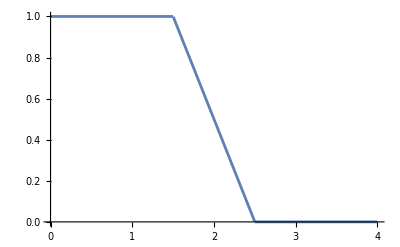

```mathematica
B:=Piecewise[{{1,0<t<1.5},{2.5-t,1.5<t<2.5},{0,2.5<t<4}}]
Plot[B,{t,0,4}]
```

```mathematica
Bc1:=Abs[FourierCoefficient[B,t,CoeffN1]]
StringForm["Fourier coefficient at 900 MHz is ``", NumberForm[Bc1,3]]
Bc2:=Abs[FourierCoefficient[B,t,CoeffN2]]
StringForm["Fourier coefficient at 2450 MHz is ``",NumberForm[Bc2,3]]
BcX:=Abs[FourierCoefficient[B,t,CoeffNX]]
StringForm["Fourier coefficient at 3900 MHz is ``",NumberForm[BcX,3]]
```

Fourier coefficient at 900 MHz is 0.00461

Fourier coefficient at 2450 MHz is 0.0018

Fourier coefficient at 3900 MHz is 0.0011

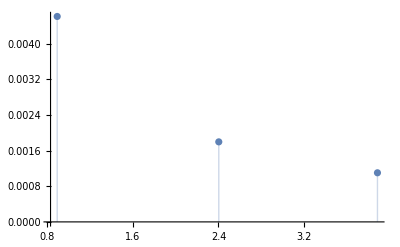

```mathematica
ListPlot[
{{pulseRate*CoeffN1,Bc1},{pulseRate*CoeffN2,Bc2},{pulseRate*CoeffNX,BcX}},Filling->Axis]
```

We now have a model and coefficients for a TIG welding AC waveform with resulting harmonics at 900 MHz, 2.4 GHz ISM, and 3900 MHz for 5G.  We can now calculate an emitted power for the arc weld at its fundamental frequency and determine appropriate emitted powers at its harmonics. The antenna gain for measurement is 5.5 dBi at 900 MHz, 8 dBi at 2.7 GHz, and 6 at 6.0 GHz.

```mathematica
pTIGdBm900dMeas:= -52+10*Log10[160*^6]-10*Log10[625*^6]
StringForm["The average power at 900 MHz assuming an average measured instantaneous power of -52 dBm, using the sample rate of 625Msps and 160 MHz of measurement bandwidth, we have `` dBm average interference power.", N[pTIGdBm900dMeas]]
```

The average power at 900 MHz assuming an average measured instantaneous power of -52 dBm, using the sample rate of 625Msps and 160 MHz of measurement bandwidth, we have -57.9176 dBm average interference power.

To determine the emitted power at 900 MHz at the welding point, we use the 3GPP path loss equation for indoor factories to back out the propagation loss and measurement antenna gain.

```mathematica
pl[f_,d_]:=31.84+21.5*Log10[d]+19.0*Log10[f]
StringForm["As a test, we should get ~40 dB of path loss at 1 m distance at 2.45 GHz, and we actually get ``",NumberForm[pl[2.412,1]],3]
```

As a test, we should get ~40 dB of path loss at 1 m distance at 2.45 GHz, and we actually get 39.1052

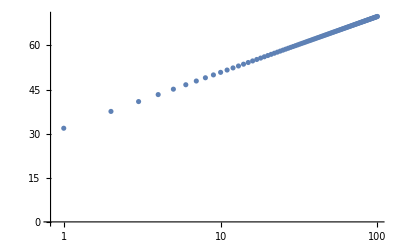

```mathematica
fList:=Range[1, 100, 1]
plListF:=pl[fList,1]
ListLogLinearPlot[Transpose[{fList,plListF}]]
```

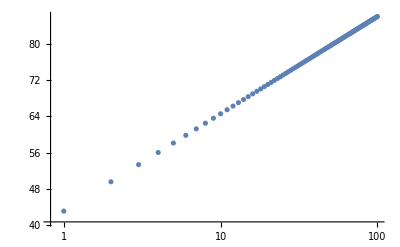

```mathematica
dList:=Range[1, 100, 1]
plListD:=pl[fX,dList]
ListLogLinearPlot[Transpose[{dList,plListD}]]
```

Now the emitted power in dBm of the arc welder at 900 MHz is determined by backing out the path loss that we calculate. We assume normal free-space propagation.

```mathematica
dTestm:=4
plTIGdB900:=pl[f1, dTestm]
pTIGdBm900Emitted:=pTIGdBm900dMeas+plTIGdB900
StringForm["Path loss at at `` GHz at `` meters is `` dB. Emitted power at the weld is `` dBm.",NumberForm[N[f1]], dTestm, ToString[N[plTIGdB900,3]], ToString[NumberForm[N[pTIGdBm900Emitted],5]]]
```

Path loss at at 0.891 GHz at 4 meters is 43.832 dB. Emitted power at the weld is -14.086 dBm.

Now, we can determine the emitted power at any desired harmonic using the power at 900 MHz as a base.  We do this for the selected harmonic fX.

```mathematica
rAmpLin:=BcX/Bc1
pTIGdBmHarmXEmitted:=pTIGdBm900Emitted+10*Log10[rAmpLin^2]
StringForm["Power 900 MHz is ``, and Power at 3900 MHz is ``", ToString[N[pTIGdBm900Emitted]],ToString[N[pTIGdBmHarmXEmitted]]]
StringForm["The ratio BcX/Bc1 is `` in dB",ToString[NumberForm[20*Log10[rAmpLin],3]]]
```

Power 900 MHz is -14.0856, and Power at 3900 MHz is -26.5156

The ratio BcX/Bc1 is -12.4 in dB

And now we can determine the interference power at the selected harmonic arriving at the interfered network device.

```mathematica
plHarmX:=N[pl[fX, dTestm]]
pTIGdBmHarmXdMeas:=pTIGdBmHarmXEmitted-plHarmX
StringForm["The expected interference power level at the Xth harmonic `` GHz at `` meters which still includes the antenna gain of the measurement equipment at the reference frequency (need to subtract this gain) is `` dBm", NumberForm[N[fX]], NumberForm[N[dTestm]], pTIGdBmHarmXdMeas]
```

The expected interference power level at the Xth harmonic 3.9 GHz at 4. meters which still includes the antenna gain of the measurement equipment at the reference frequency (need to subtract this gain) is -82.5301 dBm

For reference, the interference power at a network device as a function of distance is shown below.

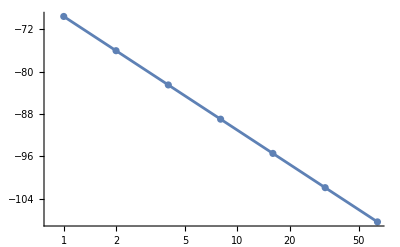

```mathematica
dTestList:=PowerRange[1,64,2]
pTIGByDistanceAtHarmfX:=pTIGdBm900Emitted-pl[fX,dTestList]+20*Log10[rAmpLin]
ListLogLinearPlot[Transpose[{dTestList,pTIGByDistanceAtHarmfX}],Joined->True, Mesh->All, GridLines->Automatic]
```

So, what is the attenuation that is needed for achieving this interference power at the network device?  It is simply the emitted interference power minus the interference power at the network device.

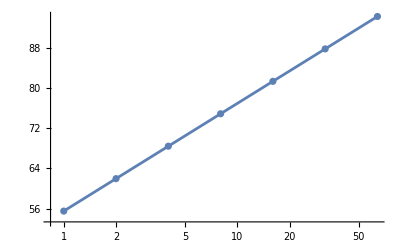

```mathematica
vAttenAtHarmX:=pTIGdBm900Emitted -pTIGByDistanceAtHarmfX
ListLogLinearPlot[Transpose[{dTestList,vAttenAtHarmX}],Joined->True, Mesh->All, GridLines->Automatic]
```